```mathematica
S0=100;s0=Log[S0];T=1;r=0.05;kappa=10;theta=0.2;sigma=0.7;rho=-0.5;v0=0.2;x0=0;alpha=3/4;eta=0.0125;Nn=8192;
PhiX[z_]:=Exp[kappa theta T (kappa - I rho sigma z)/sigma^2+I z T r + I z x0]/(Cosh[gamma[z] T /2]+ (kappa - I rho sigma z)/gamma [z]Sinh[gamma[z] T / 2])^(2 kappa theta / sigma^2)*Exp[-(z^2+I z)v0/(gamma[z] Coth[gamma[z] T/2]+kappa - I rho sigma z)]Exp[I s0 z]
```

```mathematica
Psi[u_]:=Exp[-r T]PhiX[u-(alpha+1)I]/(alpha^2+alpha-u^2+I(2alpha+1)u)
```

```mathematica
v[j_]:=eta j ;
```

```mathematica
x[j_]:=Exp[I(1/2Nn Zee-s0)v[j]]Psi[v[j]]
```

```mathematica
Zee=2Pi/(Nn eta);
```

```mathematica
kw[u_]:=-1/2Nn Zee+Zee u + s0;
```

```mathematica
CT[u_]:=Re[Exp[-alpha kw[u]]/Pi Sum[Exp[-I Zee eta j u]x[j] eta ,{j,0,Nn-1}]]
```

```mathematica
gamma[z_]:= Sqrt[sigma^2(z^2+I z)+(kappa - I rho sigma z)^2]
```

```mathematica
Exp[kw[3973]]
```

0.0527593

```mathematica
CT2[kw[Nn/2]]
```

19.6876

```mathematica
CT2[k_]:=Exp[-alpha k]/Pi Re[NIntegrate[Exp[-I u k]Psi[u],{u,0,100}]]
```

```mathematica
CT2[kw[3973]]
```

99.9496

```mathematica
MathCT = Table[{Exp[kw[j]],CT2[kw[j]]},{j,3973, 4111}]
```

{{0.0527593,99.9496},{0.0560979,99.9465},{0.0596479,99.9433},{0.0634224,99.9398},{0.0674359,99.936},{0.0717033,99.9319},{0.0762407,99.9275},{0.0810653,99.9228},{0.0861951,99.9179},{0.0916496,99.9128},{0.0974493,99.9073},{0.103616,99.9015},{0.110173,99.8953},{0.117145,99.8886},{0.124558,99.8815},{0.13244,99.8739},{0.140821,99.866},{0.149732,99.8575},{0.159207,99.8486},{0.169282,99.839},{0.179994,99.8288},{0.191384,99.818},{0.203495,99.8064},{0.216373,99.7941},{0.230065,99.7811},{0.244624,99.7673},{0.260104,99.7526},{0.276563,99.737},{0.294064,99.7203},{0.312673,99.7026},{0.332459,99.6837},{0.353497,99.6637},{0.375867,99.6424},{0.399652,99.6198},{0.424942,99.5958},{0.451833,99.5702},{0.480426,99.543},{0.510827,99.5141},{0.543153,99.4833},{0.577524,99.4506},{0.61407,99.4159},{0.652929,99.3789},{0.694247,99.3396},{0.738179,99.2978},{0.784892,99.2534},{0.834561,99.2061},{0.887372,99.1559},{0.943526,99.1025},{1.00323,99.0457},{1.06672,98.9853},{1.13422,98.9211},{1.206,98.8528},{1.28231,98.7802},{1.36346,98.703},{1.44974,98.621},{1.54148,98.5337},{1.63903,98.4409},{1.74274,98.3423},{1.85303,98.2374},{1.97029,98.1258},{2.09497,98.0072},{2.22754,97.8811},{2.3685,97.747},{2.51838,97.6044},{2.67775,97.4529},{2.8472,97.2917},{3.02737,97.1203},{3.21894,96.938},{3.42264,96.7443},{3.63923,96.5383},{3.86952,96.3192},{4.11439,96.0863},{4.37475,95.8386},{4.65159,95.5753},{4.94594,95.2953},{5.25893,94.9976},{5.59172,94.681},{5.94556,94.3444},{6.3218,93.9865},{6.72185,93.606},{7.14722,93.2014},{7.5995,92.7711},{8.0804,92.3137},{8.59174,91.8273},{9.13543,91.3101},{9.71353,90.7602},{10.3282,90.1755},{10.9818,89.5538},{11.6767,88.8928},{12.4156,88.19},{13.2013,87.4427},{14.0367,86.6481},{14.9249,85.8033},{15.8694,84.9051},{16.8736,83.9502},{17.9414,82.9349},{19.0768,81.8557},{20.284,80.7084},{21.5675,79.4891},{22.9324,78.1934},{24.3835,76.8167},{25.9265,75.3544},{27.5672,73.8017},{29.3117,72.154},{31.1665,70.4063},{33.1388,68.5543},{35.2358,66.5935},{37.4656,64.5204},{39.8364,62.3318},{42.3573,60.0259},{45.0377,57.602},{47.8877,55.0612},{50.9181,52.4069},{54.1402,49.6449},{57.5663,46.7838},{61.2091,43.8358},{65.0825,40.8163},{69.201,37.7446},{73.5801,34.6434},{78.2363,31.5389},{83.1871,28.4599},{88.4513,25.4372},{94.0485,22.5026},{100.,19.6876},{106.328,17.022},{113.057,14.5326},{120.211,12.2416},{127.818,10.166},{135.906,8.3161},{144.507,6.69579},{153.651,5.30209},{163.374,4.12583},{173.713,3.15251},{184.705,2.36348},{196.394,1.7373},{208.822,1.25117},{222.036,0.882213},{236.087,0.608637},{251.027,0.410581}}

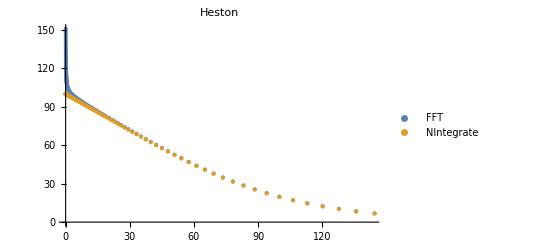

```mathematica
ListPlot[{FFT, MathCT},PlotLabel->"Heston", PlotLegends->{"FFT", "NIntegrate"},ImageSize->Full]
```

```mathematica
Xx = Table[{FFT[[All,1]][[j]],Abs[1-FFT[[All, 2]][[j]]/MathCT[[All, 2]][[j]]]},{j,1,Length[FFT[[All, 2]]]}]
```

{{0.052759,0.512272},{0.056098,0.489247},{0.059648,0.467256},{0.063422,0.446255},{0.067436,0.4262},{0.071703,0.407048},{0.076241,0.388759},{0.081065,0.371292},{0.086195,0.35461},{0.09165,0.338678},{0.097449,0.323462},{0.103616,0.308931},{0.110173,0.295054},{0.117145,0.281803},{0.124558,0.269149},{0.13244,0.257063},{0.140821,0.245521},{0.149732,0.234498},{0.159207,0.22397},{0.169282,0.213917},{0.179994,0.204317},{0.191384,0.195149},{0.203495,0.186394},{0.216373,0.178032},{0.230065,0.170047},{0.244624,0.162421},{0.260104,0.155139},{0.276563,0.148184},{0.294064,0.141543},{0.312673,0.135201},{0.332459,0.129145},{0.353497,0.123361},{0.375867,0.117838},{0.399652,0.112563},{0.424942,0.107526},{0.451833,0.102717},{0.480426,0.0981237},{0.510827,0.0937378},{0.543153,0.0895496},{0.577524,0.0855501},{0.61407,0.0817308},{0.652929,0.0780837},{0.694247,0.0746012},{0.738179,0.0712759},{0.784892,0.0681007},{0.834561,0.0650689},{0.887372,0.0621738},{0.943526,0.0594094},{1.00323,0.0567698},{1.06672,0.0542495},{1.13422,0.0518432},{1.206,0.0495457},{1.28231,0.0473521},{1.36346,0.0452578},{1.44974,0.0432582},{1.54148,0.0413492},{1.63903,0.0395266},{1.74274,0.0377867},{1.85303,0.0361257},{1.97029,0.0345401},{2.09497,0.0330266},{2.22754,0.0315818},{2.3685,0.0302027},{2.51838,0.0288864},{2.67775,0.0276301},{2.8472,0.0264311},{3.02737,0.0252869},{3.21894,0.024195},{3.42264,0.0231531},{3.63923,0.0221589},{3.86952,0.0212104},{4.11439,0.0203055},{4.37475,0.0194424},{4.65159,0.0186191},{4.94594,0.0178339},{5.25893,0.0170852},{5.59172,0.0163713},{5.94557,0.0156907},{6.32181,0.0150421},{6.72185,0.0144239},{7.14722,0.013835},{7.5995,0.013274},{8.0804,0.0127398},{8.59174,0.0122313},{9.13543,0.0117473},{9.71353,0.0112869},{10.3282,0.0108492},{10.9818,0.0104332},{11.6767,0.010038},{12.4156,0.00966293},{13.2013,0.00930719},{14.0367,0.00897009},{14.9249,0.00865099},{15.8694,0.0083493},{16.8736,0.00806448},{17.9414,0.00779605},{19.0768,0.00754358},{20.284,0.0073067},{21.5675,0.00708511},{22.9324,0.00687858},{24.3835,0.00668693},{25.9265,0.0065101},{27.5672,0.0063481},{29.3117,0.00620104},{31.1665,0.00606913},{33.1388,0.00595275},{35.2358,0.00585241},{37.4656,0.00576878},{39.8364,0.00570276},{42.3573,0.00565548},{45.0377,0.0056284},{47.8877,0.0056233},{50.9181,0.00564236},{54.1402,0.0056884},{57.5663,0.00576477},{61.2091,0.00587575},{65.0825,0.0060266},{69.201,0.00622396},{73.5801,0.00647609},{78.2363,0.00679364},{83.1871,0.00719001},{88.4513,0.00768259},{94.0485,0.00829388},{100.,0.00905341},{106.328,0.0100002},{113.057,0.0111864},{120.211,0.0126826},{127.818,0.0145852},{135.906,0.0170277},{144.507,0.0201971},{153.651,0.0243588},{163.374,0.0298955},{173.713,0.0373657},{184.705,0.0475986},{196.394,0.0618419},{208.822,0.0820082},{222.036,0.111074},{236.087,0.153759},{251.027,0.217678}}

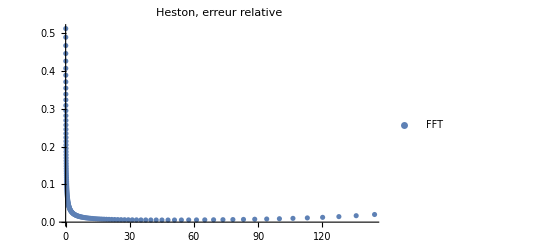

```mathematica
ListPlot[Xx,PlotLabel->"Heston, erreur relative", PlotLegends->{"FFT", "NIntegrate"},ImageSize->Full]
```

```mathematica
kw[Nn/2+1]
```

4.66653

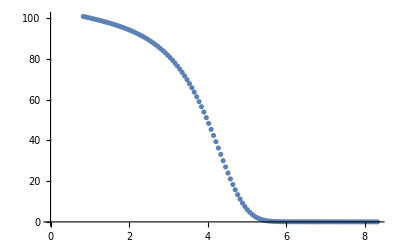

```mathematica
ListPlot[Table[{kw[j],CT[j]},{j,1.97Nn/4,2.03Nn/4}]]
```

```mathematica
FFT = {{0.052759,151.151044},{0.056098,148.845012},{0.059648,146.642353},{0.063422,144.538397},{0.067436,142.528680},{0.071703,140.608941},{0.076241,138.775106},{0.081065,137.023283},{0.086195,135.349754},{0.091650,133.750966},{0.097449,132.223525},{0.103616,130.764186},{0.110173,129.369848},{0.117145,128.037547},{0.124558,126.764450},{0.132440,125.547850},{0.140821,124.385156},{0.149732,123.273894},{0.159207,122.211695},{0.169282,121.196294},{0.179994,120.225524},{0.191384,119.297314},{0.203495,118.409678},{0.216373,117.560718},{0.230065,116.748616},{0.244624,115.971628},{0.260104,115.228088},{0.276563,114.516396},{0.294064,113.835018},{0.312673,113.182484},{0.332459,112.557383},{0.353497,111.958359},{0.375867,111.384110},{0.399652,110.833386},{0.424942,110.304982},{0.451833,109.797739},{0.480426,109.310542},{0.510827,108.842312},{0.543153,108.392012},{0.577524,107.958635},{0.614070,107.541211},{0.652929,107.138797},{0.694247,106.750481},{0.738179,106.375376},{0.784892,106.012617},{0.834561,105.661364},{0.887372,105.320794},{0.943526,104.990103},{1.003233,104.668503},{1.066718,104.355220},{1.134221,104.049489},{1.205996,103.750557},{1.282312,103.457679},{1.363458,103.170115},{1.449739,102.887128},{1.541479,102.607985},{1.639025,102.331949},{1.742744,102.058283},{1.853026,101.786244},{1.970287,101.515085},{2.094969,101.244046},{2.227540,100.972358},{2.368501,100.699238},{2.518381,100.423886},{2.677746,100.145484},{2.847196,99.863193},{3.027369,99.576149},{3.218944,99.283461},{3.422641,98.984209},{3.639228,98.677440},{3.869522,98.362166},{4.114388,98.037356},{4.374750,97.701939},{4.651588,97.354796},{4.945944,96.994759},{5.258927,96.620603},{5.591716,96.231045},{5.945565,95.824738},{6.321805,95.400267},{6.721854,94.956143},{7.147218,94.490799},{7.599500,94.002581},{8.080403,93.489747},{8.591737,92.950458},{9.135429,92.382768},{9.713526,91.784626},{10.328206,91.153858},{10.981783,90.488167},{11.676720,89.785121},{12.415632,89.042145},{13.201303,88.256515},{14.036692,87.425345},{14.924946,86.545582},{15.869408,85.613994},{16.873637,84.627165},{17.941415,83.581487},{19.076762,82.473154},{20.283955,81.298162},{21.567540,80.052313},{22.932351,78.731218},{24.383529,77.330320},{25.926538,75.844920},{27.567191,74.270220},{29.311665,72.601387},{31.166531,70.833639},{33.138774,68.962365},{35.235823,66.983273},{37.465574,64.892584},{39.836426,62.687271},{42.357307,60.365340},{45.037712,57.926163},{47.887735,55.370845},{50.918109,52.702622},{54.140248,49.927276},{57.566287,47.053520},{61.209128,44.093349},{65.082492,41.062288},{69.200964,37.979513},{73.580057,34.867784},{78.236263,31.753170},{83.187117,28.664505},{88.451265,25.632607},{94.048533,22.689235},{100.000000,19.865851},{106.328081,17.192248},{113.056608,14.695149},{120.210922,12.396876},{127.817966,10.314236},{135.906390,8.457707},{144.506657,6.831030},{153.651155,5.431244},{163.374325,4.249174},{173.712784,3.270306},{184.705470,2.475979},{196.393781,1.844743},{208.821739,1.353777},{222.036148,0.980204},{236.086775,0.702221},{251.026537,0.499955}};
```

```mathematica
CT2[
```